# PeerMind

## Statistical Quorum

### Theoretical Framework:

Background:

A population of voters needs to collectively decide whether or not to take action on an item.  In order to democratically take action, the population needs to have a {simple, super}-majority of “yes” votes.  We do not want to poll the entire population, but we do want to be certain (specifically, 95% certain) that the population does not take undesired actions.

Problem Statement:

We wish to compute the probability that the bias in a population towards voting “yes” is greater than some fraction of the population (e.g., 50% for a simple majority, 67% for a super majority, 90% for a consensus).

Assumptions:

We assume that there is a fixed underlying bias in the population that is to be estimated given raw voting data.

Without any votes, we assume that this bias may be any value between 0% and 100% with equal probability.

Voting:

We allow for score voting where each member of the population may choose any real number in the range [-1,+1] to represent their vote, with -1 representing opposition and +1 representing support.

We allow voters to "abstain" from voting.  We treat abstentions as indicating that a voter is removing themselves from the population of voters for an item.  It is important to distinguish an "abstention" (removing yourself from the voting population) from voting "0" (indicating indifference).

Bayesian Theory:

To properly understand the Bayesian approach to parameter estimation, read the following instructive tutorial: http://www.behind-the-enemy-lines.com/2008/01/are-you-bayesian-or-frequentist-or.html

The above tutorial is very similar to the problem we have at hand.  The commonplace and convenient choice of using the Beta distribution as our prior on the population bias is a consequence of its conjugacy with the binomial distribution, which arises naturally when sampling from a finite population.

After extracting the critical information from raw votes, namely the average score and the number of abstentions, we can adjust the effective population size and corresponding threshold, as well as calculate the effective number of “yes” and “no” votes, which you can think of as Heads and Tails in the aforementioned tutorial.

Deriving our expression of interest now immediately follows:

Let N=effective population size,i.e. population size - number of abstentions,
T=f×N , where c corresponds to the fraction of the population that needs to vote "yes", e.g. f=1/2 for a simple majority,
a=number of effective "yes" votes recorded,i.e., Mean[(votes+1)/2]*(number of Votes),
b=number of effective "no" votes recorded, i.e., (number of Votes - a),
K=number of remaining votes to be cast,i.e. N-a-b,
m=the minimum number of future "yes" votes needed  in order to surpass T,i.e. ⌈T-a⌉,
p=true underlying population bias

ℙ(∑"yes" ≥T|votes)
=∫_p ℙ(∑"yes" ≥T|p)×ℙ(p|votes)ⅆp
=∫_0^1 ℙ(∑"yes" ≥T|p)×Beta(p;a+1,b+1)ⅆp
=∫_0^1 (∑_(i=m)^K (K
i)(p^i(1-p))^(K-i))×Beta(p;a+1,b+1)ⅆp
=∑_(i=m)^K (K
i)∫_0^1 (p^i(1-p))^(K-i)·Beta(p;a+1,b+1)ⅆp

We can numerically computer the above expression.  In order to be certain before taking actions, we would like for the computed value to be ≥ 95%.

Done.

### Code:

```mathematica
initializePopulation[size_,majority_:"simple"]:=(
(*Computes proper threshold to satisfy for the given vote majority type*)
populationSize=size;
voteType=majority;
Which[
majority=="simple",threshold=0.5*populationSize,
majority=="super",threshold=2./3*populationSize,
majority=="consensus",threshold=0.9*populationSize
];
)

createVotes[compressedVotes_]:=(
(*Takes in a list of {score,freq} pairs that it uncompresses into a list of actual votes.*)
votes=Flatten[Table[
{score,freq}=item;
Table[If[score=="abstain","abstain",N[score]],{freq}]
,{item,compressedVotes}]]
)

computeVoteStatistics[]:=(
(*Extracts required information from raw votes and stores them as global variables*)
abstentions=Count[votes,"abstain"];
initializePopulation[populationSize-abstentions,voteType];
nonAbstentions=DeleteCases[votes,"abstain"];
numVoters=Length[nonAbstentions];
yes=Mean[(nonAbstentions+1)/2]*numVoters;
no=numVoters-yes;
yesVotesNeeded=Ceiling[threshold-yes];
remainingVoters=populationSize-numVoters;
)

computeCredibility[]:=(
(*Computes the probability associated with the true bias in the population being greater than the necessary threshold to take action.*)
{a,b}={1,1};(*{1,1} corresponds to a uniform prior*)
prior[p_]:=PDF[BetaDistribution[yes+a,no+b],p];
credibility=Sum[Binomial[remainingVoters,numYes]*Integrate[p^(numYes)*(1-p)^(remainingVoters-numYes)*prior[p],{p,0,1}],{numYes,yesVotesNeeded,remainingVoters}];
credibility
)
```

#### Example: Simple Majority

```mathematica
c=Table[
initializePopulation[140,"simple"];
createVotes[{{1,i},{-1,10},{"abstain",5}}];
computeVoteStatistics[];
{i,computeCredibility[]},{i,0,25}];
```

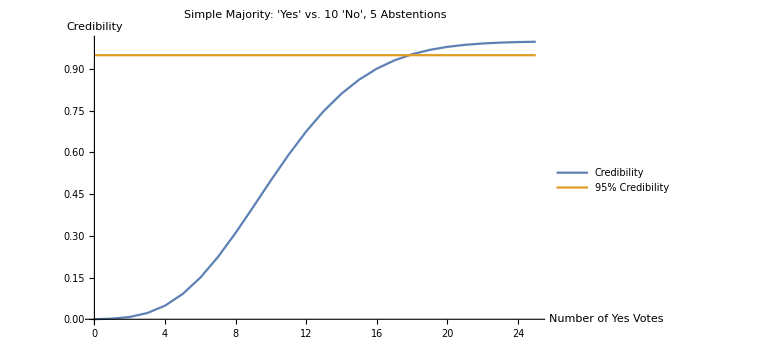

```mathematica
ListPlot[{c,Table[{i[[1]],0.95},{i,c}]},Joined->True,PlotLabel->"Simple Majority: 'Yes' vs. 10 'No', 5 Abstentions",AxesLabel->{"Number of Yes Votes","Credibility"},PlotLegends->{"Credibility","95% Credibility"},ImageSize->Large]
```

#### Example: Super Majority

```mathematica
c=Table[
initializePopulation[140,"super"];
createVotes[{{1,i},{-1,10},{"abstain",5}}];
computeVoteStatistics[];
{i,computeCredibility[]},{i,10,35}];
```

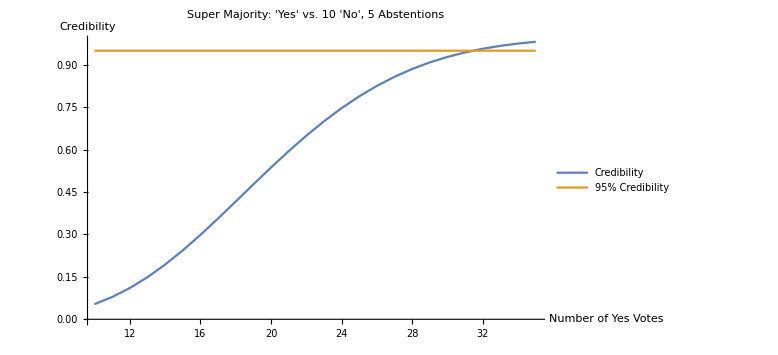

```mathematica
ListPlot[{c,Table[{i[[1]],0.95},{i,c}]},Joined->True,PlotLabel->"Super Majority: 'Yes' vs. 10 'No', 5 Abstentions",AxesLabel->{"Number of Yes Votes","Credibility"},PlotLegends->{"Credibility","95% Credibility"},ImageSize->Large]
```

### To Do

Competing Motions

We already have a method to compare two items (yes vs. no).  From this method, we can get a credible interval on option 1 beating option 2.

Now to extend this to multiple items:
Probability (X_1 beats X_2, X_3, X_4, ..., X_M) = P(X_1 beats X_2) * P(X_1 beats X_3) * ... * P(X_1 beats X_M), by independence (which is true since every voter gets to allocate between [-1,1]  for each item).
So that would be our new probability that we want to be greater than some threshold.  These computations are a little more complicated because you need to compare two items, so they will involve two for-loops per comparison.  Also, these will credibilities will be smaller in magnitude, so we might need to fine tune some parameters to make the 90% threshold still applicable.

I do not think all agenda items should be allowed to have competing motions like this because it’s more appropriate for when there is a spectrum of options that cannot be refined down to a unified motion (e.g. allocating a certain amount of money, voting amongst many candidates).  Otherwise, consensus techniques are best.

## Delegation

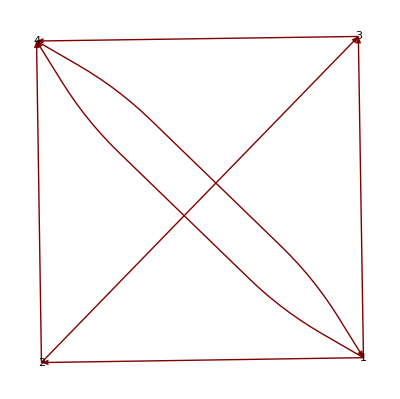

```mathematica
GraphPlot[{{1->2,.25},{2->3,.25},{2->4,.25},{3->4,.5},{1->3,.25},{4->1,.5},{1->4,.5}},VertexLabeling->True,DirectedEdges->True]
```

```mathematica
W={{0,.25,.25,.5},{0,0,.25,.25},{0,0,0,.5},{.5,0,0,0}};W//MatrixForm
```

(0 | 0.25 | 0.25 | 0.5
0 | 0 | 0.25 | 0.25
0 | 0 | 0 | 0.5
0.5 | 0 | 0 | 0)

```mathematica
votes={-1,.5,0,0};
W=Join[Wᵀ,{votes}]ᵀ;W//MatrixForm
```

(0 | 0.25 | 0.25 | 0.5 | -1
0 | 0 | 0.25 | 0.25 | 0.5
0 | 0 | 0 | 0.5 | 0
0.5 | 0 | 0 | 0 | 0)

```mathematica
W=Join[W,{{0,0,0,0,1}}];W//MatrixForm
```

(0 | 0.25 | 0.25 | 0.5 | -1
0 | 0 | 0.25 | 0.25 | 0.5
0 | 0 | 0 | 0.5 | 0
0.5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
votes=Join[votes,{0}]
```

{-1,0.5,0,0,0}

```mathematica
Eigensystem[W,1]//Chop
```

{{1.},{{-0.729243,0.130222,-0.182311,-0.364622,0.53391}}}

```mathematica
%[[2]]//MatrixForm
```

(-0.729243 | 0.130222 | -0.182311 | -0.364622 | 0.53391)

```mathematica
Mean[%ᵀ]
```

{-0.122409}

Ok I think this is the solution:

I will demonstrate how this works by a toy example:
x_1 = x_2
x_2 = 0.5 x_2 + 0.5 x_3
x_3 = x_4
x_4 = 0.25 x_1 + 0.25 x_2 + 0.25 x_3 + 0.25 x_4
where these equations describe how each voter x_i delegates their vote to the population (including to themselves).

Now set up the following matrix:
Let each row correspond to voter x_i, and each column correspond to their delegation weight, with one caveat.  That caveat is that, if the voter has delegated a portion of their vote to themselves, put that portion multiplied by their current vote (or 0 if they have not voted) in an extra column at the end of the matrix.  So the diagonal of the matrix should always be all zeros.  Finally, add one final row at the bottom that corresponds to all zeros, with a 1 in the last column.
So you get a 5x5 matrix that looks like this.

Now to do your iterative algorithm, we simply take this matrix and multiple it by the vector of inputted votes so far.
Let’s say x_1 has not voted, x_2 has voted -1, x_3 voted 1, x_4 voted 1. 
Then we make the vector (0, -1, 1, 1, 1) as our current state. (We have appended an extra 1 to make 5 total entries).

So what happens when we multiply the matrix by the current state? We get this. Notice that this is what you would get if you ran the iterative algorithm for one step.  We look at the first four entries: (-1, 0, 1, 1/4), which are all correct and take into account people who have already voted.  Also note that we replaced that last column in the matrix with the appropriate values based on the initial state votes.

So now instead of iteratively running the algorithm, there is a theoretical result that tells us that the convergent state will simply be the eigenvector of that 5x5 matrix that corresponds to eigenvalue = 1.  So we do this.  And our final result is that the votes are: (-0.5, -0.5, 0, 0).

The last row/column in the matrix and the last row in the state vector can be ignored when interpreting calculations — they are just for making dimensionality purposes.

Sound good?  I am not 100% sure yet if these matrices will have exactly one eigenvalue of 1; I think because we are replacing people who have not voted yet with a vote of “0” here, you will always get a unique solution.  If we chose to leave their vote as some “unknown”, then this will not be solvable in general I think.

You are right that my previous method allowed voters to delegate to others such that even if they vote, it may not count.  This was stupid, but I included it to keep things simple.  The better way to implement what I had proposed would be to just adjust so that if you see someone has already voted, then you ignore all of their delegation stuff and replace their row in the matrix with [0 ... 0 1]. (This was for when I said all diagonal elements are 0 and you add extra column to matrix corresponding to “self-delegation”.)

Also, for abstentions, 

Are you basically finding where a delegate has abstained, removing their % of vote, and then renormalizing?

So if x_1 = .5 x_2 + .5 x_3, and x_3=abstain, then x_1 = x_2?

And what happens if a vote cannot be determined by delegates?  Then they count as no vote, right? In my toy example, I replaced no vote with ‘0’, but that is not what you want to do b/c voting ‘0’ is not the same as not having voted yet, so this was the additional thing to tweak with my approach.

```mathematica
{{0,1,0,0,0*a},{0,0,1/2,0,1/2 b},{0,0,0,1,0*c},{1/4,1/4,1/4,0,1/4*d},{0,0,0,0,1}}//MatrixForm
```

{{0, 1, 0, 0, 0}, {0, 0, 1/2, 0, -1/2}, {0, 0, 0, 1, 0}, {1/4, 1/4, 1/4, 0, 1/4}, {0, 0, 0, 0, 1}}*{0, -1, 1, 1, 1}

Eigensystem[{{0, 1, 0, 0, 0}, {0, 0, 1/2, 0, -1/2}, {0, 0, 0, 1, 0}, {1/4, 1/4, 1/4, 0, 1/4}, {0, 0, 0, 0, 1}}]

## Online Platform UI/UX Features

Refining the user homepage:

Need to show simple statistic on how many motions they have voted on of the total (I think this will be an important tool for eventually incentivizing participation, e.g. if you don’t vote in 50% of motions by end of semester, -2 hours workshift, or +2 hours if you do, idk.)

“RSS / News” feed: what new comments/motions have been made since you last checked (like facebook notifications basically).

Personalized Discussion dashboard showing # of unread comments, statistical quorum confidence level, vote tally.

Admin organizational tools:

Label motions under categories (use of space, mural, etc.).  All users should be able to label. Admin should be able to assign specific council label to when that motion got finalized.

Closing/archiving of motions.

Searching archived motions by date/label/council

Finalizing result of motion (secretary will do this, but there needs to be a specific feature/box dedicated to documenting the end outcome)

Other:

Autolink URLs

Live Voting section.